{{5.74,38.5},{22.61,66.2},{25.73,75.4},{35.69,93.7}}

FittedModel[-718.229+8.44159 x]

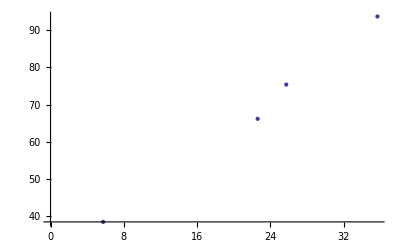

```mathematica
(*Clear unused stuff*)
Clear[ Filename, Filepath, rawBackground, rawData, BackgroundTime, DataTime, removeBackground];

(*Specify folder structure and filenames*)
Filename = "fwhm";
Filepath = NotebookDirectory[]<>"../data/";

(*Import raw data from .Spe files*)
rawData = Drop[Import[Filepath<> Filename <>".txt", "Table"],1]

fit=LinearModelFit[rawData,x,x]


Show[ListPlot[rawData], Plot[ fit[x],  {x,0,40}]]
```